#### Notebook Description

This notebook is for brain storming.

#### Project Goals

Construct a symbolic representation of a chessboard state (ChessState) and chess moves (ChessMove) in the Wolfram Language.
Develop a function which takes a ChessState and a ChessPlay and returns the new ChessState.
Build a ConvertChessNotation function for converting between the Wolfram and the algebraic chess notation.
Curate a Chess Dataset of famous chess games in the history for the data repository.
Create a ChessStatePlot function which plots a given ChessState on a chessboard. 
Create a ChessMovePlot function that plots the transition from the inputted ChessState to the next state specified by a ChessMove, alongside with a ChessAnimate function that animates a chess game (a dataset or a list of ChessMove’s).
Depending on the amount of remaining time, write a ListGameMove function that receives a ChessState (and ChessRules) and outputs all the possible ChessMove’s. 
Potentially, provide Evaluate → True/”Best” option for ListChessMove which returns sorted and associate predicted winning probabilities/scores for white using an external game engine.
Note: This project will be done keeping in mind that eventually the word Chess in the above functions would be replaced by the word Game, generalizing to as many board and card games possible.

### Chess Pieces

#### Chess Piece Names

```mathematica
If[
	NotebookDirectory[] ≠ ""
	, 
	packageDir = NotebookDirectory[];
	,
	packageDir = $InputFileName;
]
packageDir
```

/home/miladiouss/MiladBox/Mathematica/WSS18/Summer2018Starter/ChessPackage/

```mathematica
pieceNamesShort = {"King", "Queen", "Rook", "Bishop", "Knight", "Pawn"};
wpn = Table["White" <> pieceName, {pieceName, pieceNamesShort}];
bpn = Table["Black" <> pieceName, {pieceName, pieceNamesShort}];
pieceNames = wpn ~Join~ bpn;
AppendTo[pieceNames, "EmptySquare"];
```

```mathematica
pieceSymbols = 
	{"♔", "♕", "♖", "♗", "♘", "♙"} ~Join~
	{"♚", "♛", "♜", "♝", "♞", "♟"} ~Join~
	{"□"};
```

```mathematica
{♔, ♕, ♖, ♗, ♘, ♙, ♚, ♛, ♜, ♝, ♞, ♟, □} = pieceSymbols;
{♔, ♕, ♖, ♗, ♘, ♙, ♚, ♛, ♜, ♝, ♞, ♟, □} = pieceNames;
```

#### Download/Load Chess Piece Images

```mathematica
If[
	FileExistsQ[packageDir <> "pieceImages.mx"]
	,
	pieceImages = Import[NotebookDirectory[] <> "pieceImages.mx"];
	Print["Chess piece images were loaded."];
	,
	piecePicLinksWiki =
		{
		"https://upload.wikimedia.org/wikipedia/commons/thumb/4/42/Chess_klt45.svg/75px-Chess_klt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/1/15/Chess_qlt45.svg/75px-Chess_qlt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/7/72/Chess_rlt45.svg/75px-Chess_rlt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/b/b1/Chess_blt45.svg/75px-Chess_blt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/7/70/Chess_nlt45.svg/75px-Chess_nlt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/4/45/Chess_plt45.svg/75px-Chess_plt45.svg.png"
		} ~Join~
		{
		"https://upload.wikimedia.org/wikipedia/commons/thumb/f/f0/Chess_kdt45.svg/75px-Chess_kdt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/4/47/Chess_qdt45.svg/75px-Chess_qdt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/f/ff/Chess_rdt45.svg/75px-Chess_rdt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/9/98/Chess_bdt45.svg/75px-Chess_bdt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/e/ef/Chess_ndt45.svg/75px-Chess_ndt45.svg.png",
		"https://upload.wikimedia.org/wikipedia/commons/thumb/c/c7/Chess_pdt45.svg/75px-Chess_pdt45.svg.png"
		};

	imagePicMotherLink = "https://marcelk.net/chess/pieces/merida/320/";
	piecePicLinks = Table["https://marcelk.net/chess/pieces/merida/320/" <> pieceName <> ".png", {pieceName, Most @ pieceNames}];

	pieceImages = 
		Import /@ piecePicLinks;
	AppendTo[pieceImages, Graphics[{Hue[0, 0, 1, 0], Rectangle[]}, ImageSize -> ImageDimensions @ First @ pieceImages]];
	Export[NotebookDirectory[]<>"pieceImages.mx",pieceImages];
	Print["Chess piece images were downloaded."];
]
```

Chess piece images were loaded.

#### Chess Piece Object

```mathematica
pieceObj = 
	MapThread[
		#1 -> <|"Image" -> #2, "SymbolicName" -> #3|>&,
		{pieceNames, pieceImages, pieceSymbols}
	];
	
pieceObj = Association @ pieceObj;
```

```mathematica
pieceObj["WhiteKing"]["Image"]
pieceObj["WhiteKing"]["SymbolicName"]
```

-Graphics-

♔

### Setups

#### Setup Initial Chess State

```mathematica
coords = ({{"a8", "b8", "c8", "d8", "e8", "f8", "g8", "h8"}, {"a7", "b7", "c7", "d7", "e7", "f7", "g7", "h7"}, {"a6", "b6", "c6", "d6", "e6", "f6", "g6", "h6"}, {"a5", "b5", "c5", "d5", "e5", "f5", "g5", "h5"}, {"a4", "b4", "c4", "d4", "e4", "f4", "g4", "h4"}, {"a3", "b3", "c3", "d3", "e3", "f3", "g3", "h3"}, {"a2", "b2", "c2", "d2", "e2", "f2", "g2", "h2"}, {"a1", "b1", "c1", "d1", "e1", "f1", "g1", "h1"}});
stateNameArray = ({{♜, ♞, ♝, ♛, ♚, ♝, ♞, ♜}, {♟, ♟, ♟, ♟, ♟, ♟, ♟, ♟}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {♙, ♙, ♙, ♙, ♙, ♙, ♙, ♙}, {♖, ♘, ♗, ♕, ♔, ♗, ♘, ♖}});
state0 = AssociationThread[Flatten[coords] -> Flatten[stateNameArray]];
state  = state0;
```

Setup ViewPoints

```mathematica
ri = 1;
rf = 8;

whiteDownTopLeft = (* a8, b8, ... *)
	Table[
			{i, j} -> Alphabet[]⟦i⟧ <> ToString[1 + rf - j],
			{i, ri, rf, 1},
			{j, ri, rf, 1}
		] //Flatten //Association;

whiteUpTopLeft = (* h1, g1, ... *)
	Table[
			{i, j} -> Alphabet[]⟦1 + rf - j⟧ <> ToString[i],
			{i, ri, rf, 1},
			{j, ri, rf, 1}
		] //Flatten //Association;
		

whiteLeftTopLeft = (* a1, a2, ... *)
	Table[
			{i, j} -> Alphabet[]⟦i⟧ <> ToString[j],
			{i, ri, rf, 1},
			{j, ri, rf, 1}
			
		] //Flatten //Association;

whiteRightTopLeft = (* h8, h7, ... *)
	Table[
			{i, j} -> Alphabet[]⟦1 + rf - i⟧ <> ToString[1 + rf - j],
			{i, ri, rf, 1},
			{j, ri, rf, 1}
		] //Flatten //Association;
		
(* Because Inset and ArrayPlot work backwards: *)
whiteDown
whiteUp;
whiteLeft;
whiteRight;
```

whiteDown

Example of extracting information from state

```mathematica
state["a1"]
state[whiteRight[{4,8}]]
```

WhiteRook

WhiteKing

Carlo’s idea:

```mathematica
ChessState[a_?AssociationQ][s_?StringQ] /; StringMatchQ[s, LetterCharacter~~DigitCharacter];
ChessState[state]["a1"];
```

```mathematica
ClearAll[state]
```

```mathematica
f[eq, "Method"->"Something"]
```

```mathematica
ChessPlot[
	state_, 
	ViewPoint_, 
	LightSquareColor_ : RGBColor[0.8, 0.5, 0.3], 
	DarekSquareColor_ : RGBColor[0.8, 0.5, 0.3]]:=
	Module[{},
		lightSquareColor = RGBColor[1.0, 0.8, 0.6];
		darkSquareColor  = RGBColor[0.8, 0.5, 0.3];

		insetList = 
			Table[
				Inset[
					pieceObj[state⟦ViewPoint[{i, j}]⟧]["Image"], 
					{i, j} - {1, 1}, 
					{i, j} - {1, 1}, 
					1
				],
				{i, 8}, 
				{j, 8}
			];
	
		dark  = RGBColor[0.8, 0.5, 0.3];
		light = RGBColor[1.0, 0.8, 0.6];

		range = Table[Mod[i+j,2],{i,8},{j,8}];

		plot = 
			ArrayPlot[
				range,
				ColorRules -> {0 -> lightSquareColor, 1 -> darkSquareColor}, 
				Epilog -> insetList
			]
	]
	
ChessPlot[state]
```

ChessPlot[<|a8→BlackRook,b8→BlackKnight,c8→BlackBishop,d8→BlackQueen,e8→BlackKing,f8→BlackBishop,g8→BlackKnight,h8→BlackRook,a7→BlackPawn,b7→BlackPawn,c7→BlackPawn,d7→BlackPawn,e7→BlackPawn,f7→BlackPawn,g7→BlackPawn,h7→BlackPawn,a6→EmptySquare,b6→EmptySquare,c6→EmptySquare,d6→EmptySquare,e6→EmptySquare,f6→EmptySquare,g6→EmptySquare,h6→EmptySquare,a5→EmptySquare,b5→EmptySquare,c5→EmptySquare,d5→EmptySquare,e5→EmptySquare,f5→EmptySquare,g5→EmptySquare,h5→EmptySquare,a4→EmptySquare,b4→EmptySquare,c4→EmptySquare,d4→EmptySquare,e4→EmptySquare,f4→EmptySquare,g4→EmptySquare,h4→EmptySquare,a3→EmptySquare,b3→EmptySquare,c3→EmptySquare,d3→EmptySquare,e3→EmptySquare,f3→EmptySquare,g3→EmptySquare,h3→EmptySquare,a2→WhitePawn,b2→WhitePawn,c2→WhitePawn,d2→WhitePawn,e2→WhitePawn,f2→WhitePawn,g2→WhitePawn,h2→WhitePawn,a1→WhiteRook,b1→WhiteKnight,c1→WhiteBishop,d1→WhiteQueen,e1→WhiteKing,f1→WhiteBishop,g1→WhiteKnight,h1→WhiteRook|>]

Carlo’s Idea:

```mathematica
wki=pieceObj["WhiteKing"]["Image"];
	bki=pieceObj["BlackKing"]["Image"];
	
	pi = {wki, bki};

	pPos = {{1,1},{2,3}};
	
	LocatorPane[
		Dynamic[pPos],
		ap,
		Appearance -> pi];
```

```mathematica
Alphabet[]⟦2⟧<>ToString[1]
```

b1

```mathematica
ClearAll[ChessPlot]
```

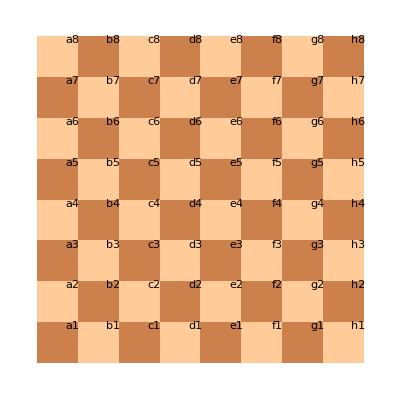

```mathematica
ChessPlot[
	state_,  
	LightSquareColor_ : RGBColor[1.0, 0.8, 0.6], 
	DarekSquareColor_ : RGBColor[0.8, 0.5, 0.3]]:=
	Module[{},
	
		emptyBoard = Table[Mod[i + j, 2], {i, 8}, {j, 8}];
		
		pieceInset =
			Table[
				Inset[
					pieceObj[state[Alphabet[]⟦i⟧ <> ToString[j]]]["Image"], 
					{i, j} - {1, 1}, 
					{i, j} - {1, 1}, 
					1
				]
				,
				{i, 8}
				, 
				{j, 8}
			];
			
		coordInset = 
			Table[
				Inset[
					Text[Style[Alphabet[]⟦i⟧ <> ToString[j],7]], 
					{i, j} + {-0.12, -0.09},
					Automatic,
					1
					]
				,
				{i, 8}
				,
				{j, 8}
				];
		
		plot = 		
			ArrayPlot[
				emptyBoard,
				ColorRules -> {0 -> LightSquareColor, 1 -> DarekSquareColor}, 
				Epilog -> pieceInset ~Join~ coordInset
			];
		
		plot
]

ChessPlot[state]
```

```mathematica
Options[fff] = {"ViewPoint" -> Automatic}
fff[OptionsPattern[]]:= Replace[OptionValue["ViewPoint"],{ Automatic|"WhiteDown" -> ({i,j}↦ Alphabet[]⟦9 - i⟧ <> ToString[9 - j])}]
```

{ViewPoint→Automatic}

```mathematica
fff["ViewPoint" -> "WhiteDown"]
```

Function[{i,j},Alphabet[]⟦9-i⟧<>ToString[9-j]]

```mathematica
fff[OptionsPattern[]] := OptionValue["ViewPoint"]
```

```mathematica
fff[]
```

OptionValue[ViewPoint]

```mathematica
state;
```

```mathematica
ChessState
```

```mathematica
↦
```

```mathematica
Lookup
```

```mathematica
pieceObj[Lookup[state, insetToAlg[i, j], "EmptySquare"]]["Image"]
```

```mathematica
Alphabet[][[;;8]]
```

{a,b,c,d,e,f,g,h}

```mathematica
Table[ToString@i,{i,8}]
```

{1,2,3,4,5,6,7,8}

{ViewPoint→Automatic}

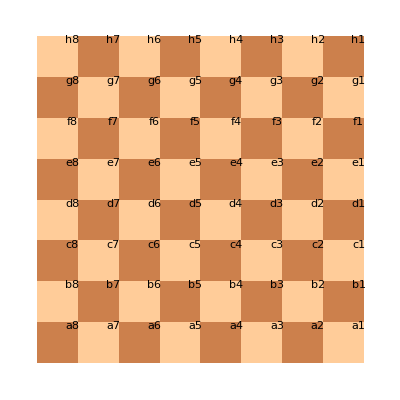

```mathematica
files = {"a", "b", "c", "d", "e", "f", "g", "h"};
ranks = {"1", "2", "3", "4", "5", "6", "7", "8"};
		
		emptyBoard = Table[Mod[i + j, 2], {i, 8}, {j, 8}];
		
		tabulatePieceInset[insetToAlgFunc_] :=
			Table[
				Inset[
					pieceObj[state[insetToAlgFunc[i, j]]]["Image"], 
					{i, j} - {1, 1}, 
					{i, j} - {1, 1}, 
					1
				]
				,
				{i, 8}
				, 
				{j, 8}
			];
			
		tabulateCoordInset[insetToAlgFunc_] := 
			Table[
				Inset[
					Text[Style[insetToAlgFunc[i, j], 7]], 
					{i, j} + {-0.12, -0.09},
					Automatic,
					1
				]
				,
				{i, 8}
				,
				{j, 8}
			];
			
			
				
Options[ChessPlot] = {"ViewPoint" -> Automatic}
ChessPlot[
	state_,
	LightSquareColor_ : RGBColor[1.0, 0.8, 0.6], 
	DarekSquareColor_ : RGBColor[0.8, 0.5, 0.3]
	] :=
	
	Module[{},
		(* ViewPoint WhiteDown, Origin is a1 *)
		insetToAlg[i_, j_] := files⟦9 - i⟧ <> ranks⟦9 - j⟧;
		(* ViewPoint WhiteUp, Origin is h8 *)
		insetToAlg[i_, j_] := files⟦i⟧ <> ranks⟦j⟧;
		(* ViewPoint WhiteLeft, Origin is h1 *)
		insetToAlg[i_, j_] := files⟦9 - j⟧ <> ranks⟦i⟧;
		(* ViewPoint WhiteRight, Origin is a8 *)
		insetToAlg[i_, j_] := files⟦j⟧ <> ranks⟦9 - i⟧;
		
		
		emptyBoard = Table[Mod[i + j, 2], {i, 8}, {j, 8}];
		
		pieceInset =
			Table[
				Inset[
					pieceObj[state[insetToAlg[i, j]]]["Image"], 
					{i, j} - {1, 1}, 
					{i, j} - {1, 1}, 
					1
				]
				,
				{i, 8}
				, 
				{j, 8}
			];
			
		coordInset = 
			Table[
				Inset[
					Text[Style[insetToAlg[i, j], 7]], 
					{i, j} + {-0.12, -0.09},
					Automatic,
					1
					]
				,
				{i, 8}
				,
				{j, 8}
				];
		
		plot = 		
			ArrayPlot[
				emptyBoard,
				ColorRules -> {0 -> LightSquareColor, 1 -> DarekSquareColor}, 
				Epilog -> pieceInset ~Join~ coordInset
			];
		
		plot
]

ChessPlot[state]
```

```mathematica
bottomLeftBlackBoard //MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

```mathematica
bottomLeftWhiteBoard //MatrixForm
```

(1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1)

-Graphics-

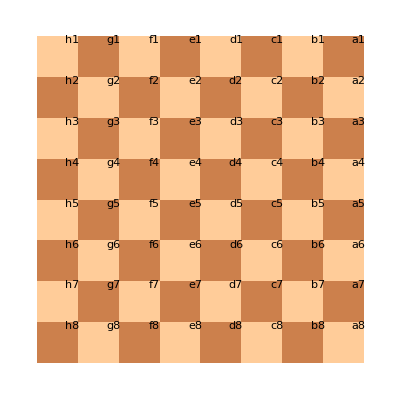

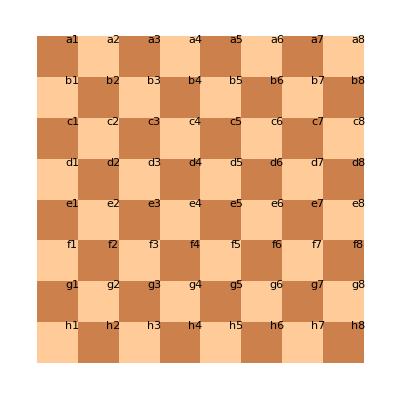

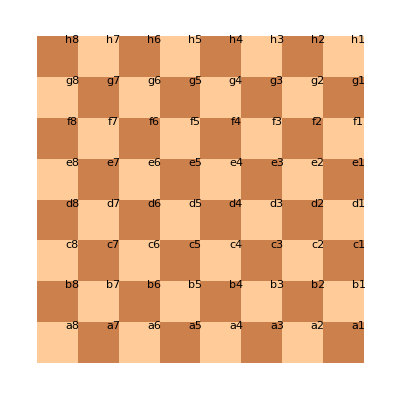

```mathematica
files = {"a", "b", "c", "d", "e", "f", "g", "h"};
ranks = {"1", "2", "3", "4", "5", "6", "7", "8"};
		
emptyBoard = Table[Mod[i + j, 2], {i, 8}, {j, 8}];
		
tabulatePieceInset[insetToAlgFunc_] :=
	Table[
		Inset[
			pieceObj[state[insetToAlgFunc[i, j]]]["Image"], 
			{i, j} - {1, 1}, 
			{i, j} - {1, 1}, 
			1
		]
		,
		{i, 8}
		, 
		{j, 8}
	];
			
tabulateCoordInset[insetToAlgFunc_] := 
	Table[
		Inset[
			Text[Style[insetToAlgFunc[i, j], 7]], 
			{i, j} + {-0.12, -0.09},
			Automatic,
			1
		]
		,
		{i, 8}
		,
		{j, 8}
	];
		

		(* ViewPoint WhiteDown, Origin is a1 *)
		whiteDownPieceTable = 
			tabulatePieceInset[{i, j} ↦ files⟦i⟧ <> ranks⟦j⟧];
		whiteDownCoordTable = 
			tabulateCoordInset[{i, j} ↦ files⟦i⟧ <> ranks⟦j⟧];
		(* ViewPoint WhiteUp, Origin is h8 *)
		whiteUpPieceTable = 
			tabulatePieceInset[{i, j} ↦ files⟦9 - i⟧ <> ranks⟦9 - j⟧];
		whiteUpCoordTable = 
			tabulateCoordInset[{i, j} ↦ files⟦9 - i⟧ <> ranks⟦9 - j⟧];
		(* ViewPoint WhiteLeft, Origin is h1 *)
		whiteLeftPieceTable = 
			tabulatePieceInset[{i, j} ↦ files⟦9 - j⟧ <> ranks⟦i⟧];
		whiteLeftCoordTable = 
			tabulateCoordInset[{i, j} ↦ files⟦9 - j⟧ <> ranks⟦i⟧];
		(* ViewPoint WhiteRight, Origin is a8 *)
		whiteRightPieceTable = 
			tabulatePieceInset[{i, j} ↦ files⟦j⟧ <> ranks⟦9 - i⟧];
		whiteRightCoordTable =
			tabulateCoordInset[{i, j} ↦ files⟦j⟧ <> ranks⟦9 - i⟧];

		bottomLeftBlackBoard = Table[Mod[i + j    , 2], {i, 8}, {j, 8}];
		bottomLeftWhiteBoard = Table[Mod[i + j + 1, 2], {i, 8}, {j, 8}];
		
Options[ChessPlot] = {"WhiteOrientation" -> Automatic};
ChessPlot[state_, OptionsPattern[]] :=
	
	Module[{},
		LightSquareColor = RGBColor[1.0, 0.8, 0.6];
		DarekSquareColor = RGBColor[0.8, 0.5, 0.3];
		
		Switch[
			OptionValue["WhiteOrientation"],
			Automatic | "Down",
				pieceInset = whiteDownPieceTable;
				coordInset = whiteDownCoordTable;
				emptyBoard = bottomLeftBlackBoard;
			,
			"Up",
				pieceInset = whiteUpPieceTable;
				coordInset = whiteUpCoordTable;
				emptyBoard = bottomLeftBlackBoard;
			,
			"Left",
				pieceInset = whiteLeftPieceTable;
				coordInset = whiteLeftCoordTable;
				emptyBoard = bottomLeftWhiteBoard;
			,
			"Right",
				pieceInset = whiteRightPieceTable;
				coordInset = whiteRightCoordTable;
				emptyBoard = bottomLeftWhiteBoard;
			,
			_
			,
			Message["Wrong ViewPoint option was provided."]; Return[$Failed];
		];
		
		plot = 		
			ArrayPlot[
				emptyBoard,
				ColorRules -> {0 -> LightSquareColor, 1 -> DarekSquareColor}, 
				Epilog -> pieceInset ~Join~ coordInset
			];
		
		plot
	]

ChessPlot[state, "WhiteOrientation" -> "Down"]
ChessPlot[state, "WhiteOrientation" -> "Up"]
ChessPlot[state, "WhiteOrientation" -> "Left"]
ChessPlot[state, "WhiteOrientation" -> "Right"]
```

```mathematica
ChessMove[ChessState, "a1"->"a5"]
```

```mathematica
img=-Graphics-;
ImageRotate[img,-180°];
```

```mathematica
pos = {{1, 1}, {2, 3}};

ArrayPlot[
		range,
		ColorRules -> {0 -> lightSquareColor, 1 -> darkSquareColor}, 
		Epilog -> 
			{
				Inset[
					pieceObj[state⟦whiteLeft[{1, 1}]⟧]["Image"], 
					pos[[1]] - {1, 1}, 
					pos[[1]] - {1, 1}, 
					0.9]
				,
				Inset[
					Rasterize["a1", Background->None, ImageResolution->250], 
					pos[[2]] + {-0.16, -0.88},
					Automatic,
					.3
					]

			}~Join~tbl2
	]
```

Part::pkspec1: The expression whiteLeft[{1,1}] cannot be used as a part specification.

-Graphics-

```mathematica
LocatorPane[
		Dynamic[pos],
		pieceObj["BlackKing"]["Image"]
	]
```

```mathematica
gameString = "1. e4 e5 2. Nf3 Nc6 3. Nc3 Nf6 4. Bb5 Bb4 5. O-O O-O 6. d3 Bxc3 7. bxc3 d6 8.
Bg5 Bd7 9. Nd2 h6 10. Bh4 g5 11. Bg3 Ne7 12. Bxd7 Nxd7 13. d4 f5 14. exf5 exd4
15. cxd4 Nxf5 16. Qf3 Rf7 17. Qxb7 Nxd4 18. Qe4 Nf5 19. Rae1 Qc8 20. f4 Nf6 21.
Qd3 g4 22. Bf2 Qd7 23. Bd4 Nxd4 24. Qxd4 Qb5 25. Kh1 Qd5 26. Qf2 Qxa2 27. Nb3 a5
28. Ra1 Qb2 29. Nxa5 Qc3 30. Nb3 Rxa1 31. Nxa1 Nd5 32. g3 Re7 33. Nb3 Re3 34.
Rd1 Nf6 35. Nd2 Qxc2 36. Qxe3 Qxd1+ 37. Kg2 Kf7 38. f5 Qa1 39. Qxh6 Qd4 40. Qg6+
Ke7 41. Qg7+ Ke8 42. Qg5 Qd5+ 43. Kg1 Kf7 44. Qg6+ Ke7 45. Qg7+ Qf7 46. Qg5 Qd5
47. Qg7+ Qf7 48. Qg5 Qd5 49. Qg7+ 1/2-1/2";

(* Remove newline *)
gameString = StringReplace[gameString,{"\n" -> ""}];

(* Remove game result *)
gameResultStrings = {"1-0", "0-1", "1/2-1/2"};
gameString = StringSplit[gameString, gameResultStrings]⟦1⟧;

(* Splite to turns *)
gs = StringSplit[gameString, DigitCharacter..~~"."];

(* Splite to moves *)
gs = StringSplit[#,WhitespaceCharacter]&/@ gs
```

{{e4,e5},{Nf3,Nc6},{Nc3,Nf6},{Bb5,Bb4},{O-O,O-O},{d3,Bxc3},{bxc3,d6},{Bg5,Bd7},{Nd2,h6},{Bh4,g5},{Bg3,Ne7},{Bxd7,Nxd7},{d4,f5},{exf5,exd},{cxd4,Nxf5},{Qf3,Rf7},{Qxb7,Nxd4},{Qe4,Nf5},{Rae1,Qc8},{f4,Nf6},{Qd3,g4},{Bf2,Qd7},{Bd4,Nxd4},{Qxd4,Qb5},{Kh1,Qd5},{Qf2,Qxa2},{Nb3,a},{Ra1,Qb2},{Nxa5,Qc3},{Nb3,Rxa1},{Nxa1,Nd5},{g3,Re7},{Nb3,Re3},{Rd1,Nf6},{Nd2,Qxc2},{Qxe3,Qxd1+},{Kg2,Kf7},{f5,Qa1},{Qxh6,Qd4},{Qg6+Ke7},{Qg7+,Ke8},{Qg5,Qd5+},{Kg1,Kf7},{Qg6+,Ke7},{Qg7+,Qf7},{Qg5,Qd},{Qg7+,Qf7},{Qg5,Qd5},{Qg7+}}

```mathematica
Flatten[Thread/@Thread[{"W","B"}->Transpose@Cases[gs,{_,_}]]]
```

{W→e4,W→Nf3,W→Nc3,W→Bb5,W→O-O,W→d3,W→bxc3,W→Bg5,W→Nd2,W→Bh4,W→Bg3,W→Bxd7,W→d4,W→exf5,W→cxd4,W→Qf3,W→Qxb7,W→Qe4,W→Rae1,W→f4,W→Qd3,W→Bf2,W→Bd4,W→Qxd4,W→Kh1,W→Qf2,W→Nb3,W→Ra1,W→Nxa5,W→Nb3,W→Nxa1,W→g3,W→Nb3,W→Rd1,W→Nd2,W→Qxe3,W→Kg2,W→f5,W→Qxh6,W→Qg7+,W→Qg5,W→Kg1,W→Qg6+,W→Qg7+,W→Qg5,W→Qg7+,W→Qg5,B→e5,B→Nc6,B→Nf6,B→Bb4,B→O-O,B→Bxc3,B→d6,B→Bd7,B→h6,B→g5,B→Ne7,B→Nxd7,B→f5,B→exd,B→Nxf5,B→Rf7,B→Nxd4,B→Nf5,B→Qc8,B→Nf6,B→g4,B→Qd7,B→Nxd4,B→Qb5,B→Qd5,B→Qxa2,B→a,B→Qb2,B→Qc3,B→Rxa1,B→Nd5,B→Re7,B→Re3,B→Nf6,B→Qxc2,B→Qxd1+,B→Kf7,B→Qa1,B→Qd4,B→Ke8,B→Qd5+,B→Kf7,B→Ke7,B→Qf7,B→Qd,B→Qf7,B→Qd5}

```mathematica
Thread
```

Thread

```mathematica
Flatten@Map[Thread[If[Length[#]==2,{"w","b"},{"w"}]->#]&,gs]
```

{w→e4,b→e5,w→Nf3,b→Nc6,w→Nc3,b→Nf6,w→Bb5,b→Bb4,w→O-O,b→O-O,w→d3,b→Bxc3,w→bxc3,b→d6,w→Bg5,b→Bd7,w→Nd2,b→h6,w→Bh4,b→g5,w→Bg3,b→Ne7,w→Bxd7,b→Nxd7,w→d4,b→f5,w→exf5,b→exd,w→cxd4,b→Nxf5,w→Qf3,b→Rf7,w→Qxb7,b→Nxd4,w→Qe4,b→Nf5,w→Rae1,b→Qc8,w→f4,b→Nf6,w→Qd3,b→g4,w→Bf2,b→Qd7,w→Bd4,b→Nxd4,w→Qxd4,b→Qb5,w→Kh1,b→Qd5,w→Qf2,b→Qxa2,w→Nb3,b→a,w→Ra1,b→Qb2,w→Nxa5,b→Qc3,w→Nb3,b→Rxa1,w→Nxa1,b→Nd5,w→g3,b→Re7,w→Nb3,b→Re3,w→Rd1,b→Nf6,w→Nd2,b→Qxc2,w→Qxe3,b→Qxd1+,w→Kg2,b→Kf7,w→f5,b→Qa1,w→Qxh6,b→Qd4,w→Qg6+Ke7,w→Qg7+,b→Ke8,w→Qg5,b→Qd5+,w→Kg1,b→Kf7,w→Qg6+,b→Ke7,w→Qg7+,b→Qf7,w→Qg5,b→Qd,w→Qg7+,b→Qf7,w→Qg5,b→Qd5,w→Qg7+}

```mathematica
Table[<|"White"->#1⟦1⟧,"Black"->#2⟦2⟧|>&@x,{x,gs⟦;;10⟧}]
```

Function::slotn: Slot number 2 in Association[White→#1⟦1⟧,Black→#2⟦2⟧]& cannot be filled from (Association[White→#1⟦1⟧,Black→#2⟦2⟧]&)[{e4,e5}].

Part::partw: Part 2 of #2 does not exist.

Function::slotn: Slot number 2 in Association[White→#1⟦1⟧,Black→#2⟦2⟧]& cannot be filled from (Association[White→#1⟦1⟧,Black→#2⟦2⟧]&)[{Nf3,Nc6}].

Function::slotn: Slot number 2 in Association[White→#1⟦1⟧,Black→#2⟦2⟧]& cannot be filled from (Association[White→#1⟦1⟧,Black→#2⟦2⟧]&)[{Nc3,Nf6}].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

{<|White→e4,Black→#2⟦2⟧|>,<|White→Nf3,Black→#2⟦2⟧|>,<|White→Nc3,Black→#2⟦2⟧|>,<|White→Bb5,Black→#2⟦2⟧|>,<|White→O-O,Black→#2⟦2⟧|>,<|White→d3,Black→#2⟦2⟧|>,<|White→bxc3,Black→#2⟦2⟧|>,<|White→Bg5,Black→#2⟦2⟧|>,<|White→Nd2,Black→#2⟦2⟧|>,<|White→Bh4,Black→#2⟦2⟧|>}